# Summary of Core Language Features added in 7.0

Peter Cullen Burbery

I look at examples from 7.0

## List & Expression Manipulation

## Gather

```mathematica
Gather[{b,c,c,d,b}]
```

{{b,b},{c,c},{d}}

```mathematica
Gather[{{b,1},{c,1},{b,2},{f,1},{c,3}},First[#1]==First[#2]&]
```

{{{b,1},{b,2}},{{c,1},{c,3}},{{f,1}}}

```mathematica
Gather[First[#1]==First[#2]&][{{b,1},{c,1},{b,2},{f,1},{c,3}}]
```

Gather[First[#1]==First[#2]&][{{b,1},{c,1},{b,2},{f,1},{c,3}}]

I thought there'd be an operator form for Gather but I guess there isn't. I think this should be implemented. I'm going to add a feature request on redmine.

## GatherBy

```mathematica
GatherBy[Range[19],OddQ]
```

{{1,3,5,7,9,11,13,15,17,19},{2,4,6,8,10,12,14,16,18}}

```mathematica
GatherBy[OddQ[#]&][Range[19]]
```

GatherBy[OddQ[#1]&][{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}]

I also thought this had an operator form but I guess it doesn't.

```mathematica
GatherBy[{{b,1},{c,1},{b,2},{f,1},{c,3}},First]
```

{{{b,1},{b,2}},{{c,1},{c,3}},{{f,1}}}

## SplitBy

```mathematica
Range[1,19,1/3]
```

{1,4/3,5/3,2,7/3,8/3,3,10/3,11/3,4,13/3,14/3,5,16/3,17/3,6,19/3,20/3,7,22/3,23/3,8,25/3,26/3,9,28/3,29/3,10,31/3,32/3,11,34/3,35/3,12,37/3,38/3,13,40/3,41/3,14,43/3,44/3,15,46/3,47/3,16,49/3,50/3,17,52/3,53/3,18,55/3,56/3,19}

```mathematica
SplitBy[Range[1,19,1/3],IntegerPart]
```

{{1,4/3,5/3},{2,7/3,8/3},{3,10/3,11/3},{4,13/3,14/3},{5,16/3,17/3},{6,19/3,20/3},{7,22/3,23/3},{8,25/3,26/3},{9,28/3,29/3},{10,31/3,32/3},{11,34/3,35/3},{12,37/3,38/3},{13,40/3,41/3},{14,43/3,44/3},{15,46/3,47/3},{16,49/3,50/3},{17,52/3,53/3},{18,55/3,56/3},{19}}

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
SplitBy[Tuples[{1,2},3],First]
```

{{{1,1,1},{1,1,2},{1,2,1},{1,2,2}},{{2,1,1},{2,1,2},{2,2,1},{2,2,2}}}

Split by the first part and then the second:

```mathematica
SplitBy[Tuples[{1,2},3],{First,Part[#,2]&}]
```

{{{{1,1,1},{1,1,2}},{{1,2,1},{1,2,2}}},{{{2,1,1},{2,1,2}},{{2,2,1},{2,2,2}}}}

```mathematica
SplitBy[Tuples[{1,2},3],{First,#[[2]]&}]
```

{{{{1,1,1},{1,1,2}},{{1,2,1},{1,2,2}}},{{{2,1,1},{2,1,2}},{{2,2,1},{2,2,2}}}}

Split dates:

```mathematica
Table[{y,m},{y,2007,2008},{m,1,12}]
```

{{{2007,1},{2007,2},{2007,3},{2007,4},{2007,5},{2007,6},{2007,7},{2007,8},{2007,9},{2007,10},{2007,11},{2007,12}},{{2008,1},{2008,2},{2008,3},{2008,4},{2008,5},{2008,6},{2008,7},{2008,8},{2008,9},{2008,10},{2008,11},{2008,12}}}

```mathematica
Table[DateString[{y,m},{"MonthName","/","Year"}],{y,2007,2008},{m,1,12}]
```

{{January/2007,February/2007,March/2007,April/2007,May/2007,June/2007,July/2007,August/2007,September/2007,October/2007,November/2007,December/2007},{January/2008,February/2008,March/2008,April/2008,May/2008,June/2008,July/2008,August/2008,September/2008,October/2008,November/2008,December/2008}}

```mathematica
Flatten@Table[DateString[{y,m},{"MonthName","/","Year"}],{y,2007,2008},{m,1,12}]
```

{January/2007,February/2007,March/2007,April/2007,May/2007,June/2007,July/2007,August/2007,September/2007,October/2007,November/2007,December/2007,January/2008,February/2008,March/2008,April/2008,May/2008,June/2008,July/2008,August/2008,September/2008,October/2008,November/2008,December/2008}

```mathematica
SplitBy[Flatten@Table[DateString[{y,m},{"MonthName","/","Year"}],{y,2007,2008},{m,1,12}],DateList[{#,{"MonthName","/","Year"}}][[1]]&]
```

{{January/2007,February/2007,March/2007,April/2007,May/2007,June/2007,July/2007,August/2007,September/2007,October/2007,November/2007,December/2007},{January/2008,February/2008,March/2008,April/2008,May/2008,June/2008,July/2008,August/2008,September/2008,October/2008,November/2008,December/2008}}

I wonder if SplitBy has an operator form:

```mathematica
SplitBy[DateList[{#,{"MonthName","/","Year"}}][[1]]&][Flatten@Table[DateString[{y,m},{"MonthName","/","Year"}],{y,2007,2008},{m,1,12}]]
```

DateList[{#1,{MonthName,/,Year}}]⟦1⟧&

```mathematica
SplitBy[DateList[{#,{"Month", "/","YearShort"}}][[1]]&][Flatten@Table[DateString[{y,m},{"Month", "/","YearShort"}],{y,2007,2008},{m,1,12}]]
```

DateList[{#1,{Month,/,YearShort}}]⟦1⟧&

I don't think this is working either. I will also submit a feature request for an operator form for SplitBy.

## DeleteDuplicates

```mathematica
DeleteDuplicates[{1,7,8,4,3,4,1,9,9,2,5}]
```

{1,7,8,4,3,9,2,5}

```mathematica
DeleteDuplicates[<|a->1,b->2,c->1,d->3,e->2|>]
```

<|a→1,b→2,d→3|>

## ArrayPad

```mathematica
ArrayPad[{1,2,3},1]
```

{0,1,2,3,0}

```mathematica
ArrayPad[IdentityMatrix[2],2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ArrayPad[HilbertMatrix[2],2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1/2 | 0 | 0
0 | 0 | 1/2 | 1/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ArrayPad[{1,2,3},{2,4}]
```

{0,0,1,2,3,0,0,0,0}

```mathematica
ArrayPad[{1,2,3},2,x]
```

{x,x,1,2,3,x,x}

```mathematica
ArrayPad[{1,2,3},2,b]
```

{b,b,1,2,3,b,b}

```mathematica
ArrayPad[{1,2,3},2,"Fixed"]
```

{1,1,1,2,3,3,3}

```mathematica
ArrayPad[HilbertMatrix[2],{{1},{5}}] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Fixed

```mathematica
m=KroneckerProduct[Sqrt[Range[6]],Sqrt[Range[6]]]
```

{{1,√2,√3,2,√5,√6},{√2,2,√6,2 √2,√10,2 √3},{√3,√6,3,2 √3,√15,3 √2},{2,2 √2,2 √3,4,2 √5,2 √6},{√5,√10,√15,2 √5,5,√30},{√6,2 √3,3 √2,2 √6,√30,6}}

```mathematica
m//MatrixForm
```

(1 | √2 | √3 | 2 | √5 | √6
√2 | 2 | √6 | 2 √2 | √10 | 2 √3
√3 | √6 | 3 | 2 √3 | √15 | 3 √2
2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6
√5 | √10 | √15 | 2 √5 | 5 | √30
√6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6)

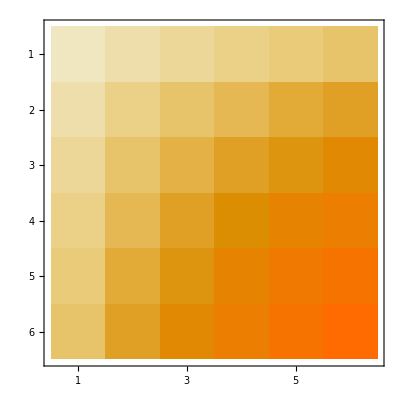

```mathematica
MatrixPlot[m]
```

```mathematica
ArrayPad[m,4,"Fixed"]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6 | √6 | √6
1 | 1 | 1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6 | √6 | √6
1 | 1 | 1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6 | √6 | √6
1 | 1 | 1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6 | √6 | √6
1 | 1 | 1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6 | √6 | √6
√2 | √2 | √2 | √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 2 √3 | 2 √3 | 2 √3 | 2 √3
√3 | √3 | √3 | √3 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 3 √2 | 3 √2 | 3 √2 | 3 √2
2 | 2 | 2 | 2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √6 | 2 √6 | 2 √6 | 2 √6
√5 | √5 | √5 | √5 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √30 | √30 | √30 | √30
√6 | √6 | √6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6 | 6 | 6
√6 | √6 | √6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6 | 6 | 6
√6 | √6 | √6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6 | 6 | 6
√6 | √6 | √6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6 | 6 | 6
√6 | √6 | √6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6 | 6 | 6)

```mathematica
ArrayPad[m,4,"Extrapolated"]//MatrixForm
```

(57-40 √2 | 44-31 √2 | 31-22 √2 | 18-13 √2 | 5-4 √2 | -8+5 √2 | 5 √3-4 √6 | 10-8 √2 | 5 √5-4 √10 | -8 √3+5 √6 | -16 √3-5 √5+10 √6+4 √10 | -24 √3-10 √5+15 √6+8 √10 | -32 √3-15 √5+20 √6+12 √10 | -40 √3-20 √5+25 √6+16 √10
44-31 √2 | 34-24 √2 | 24-17 √2 | 14-10 √2 | 4-3 √2 | -6+4 √2 | 4 √3-3 √6 | 8-6 √2 | 4 √5-3 √10 | -6 √3+4 √6 | -12 √3-4 √5+8 √6+3 √10 | -18 √3-8 √5+12 √6+6 √10 | -24 √3-12 √5+16 √6+9 √10 | -30 √3-16 √5+20 √6+12 √10
31-22 √2 | 24-17 √2 | 17-12 √2 | 10-7 √2 | 3-2 √2 | -4+3 √2 | 3 √3-2 √6 | 6-4 √2 | 3 √5-2 √10 | -4 √3+3 √6 | -8 √3-3 √5+6 √6+2 √10 | -12 √3-6 √5+9 √6+4 √10 | -16 √3-9 √5+12 √6+6 √10 | -20 √3-12 √5+15 √6+8 √10
18-13 √2 | 14-10 √2 | 10-7 √2 | 6-4 √2 | 2-√2 | -2+2 √2 | 2 √3-√6 | 4-2 √2 | 2 √5-√10 | -2 √3+2 √6 | -4 √3-2 √5+4 √6+√10 | -6 √3-4 √5+6 √6+2 √10 | -8 √3-6 √5+8 √6+3 √10 | -10 √3-8 √5+10 √6+4 √10
5-4 √2 | 4-3 √2 | 3-2 √2 | 2-√2 | 1 | √2 | √3 | 2 | √5 | √6 | -√5+2 √6 | -2 √5+3 √6 | -3 √5+4 √6 | -4 √5+5 √6
-8+5 √2 | -6+4 √2 | -4+3 √2 | -2+2 √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 4 √3-√10 | 6 √3-2 √10 | 8 √3-3 √10 | 10 √3-4 √10
5 √3-4 √6 | 4 √3-3 √6 | 3 √3-2 √6 | 2 √3-√6 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 6 √2-√15 | 9 √2-2 √15 | 12 √2-3 √15 | 15 √2-4 √15
10-8 √2 | 8-6 √2 | 6-4 √2 | 4-2 √2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | -2 √5+4 √6 | -4 √5+6 √6 | -6 √5+8 √6 | -8 √5+10 √6
5 √5-4 √10 | 4 √5-3 √10 | 3 √5-2 √10 | 2 √5-√10 | √5 | √10 | √15 | 2 √5 | 5 | √30 | -5+2 √30 | -10+3 √30 | -15+4 √30 | -20+5 √30
-8 √3+5 √6 | -6 √3+4 √6 | -4 √3+3 √6 | -2 √3+2 √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 12-√30 | 18-2 √30 | 24-3 √30 | 30-4 √30
-16 √3-5 √5+10 √6+4 √10 | -12 √3-4 √5+8 √6+3 √10 | -8 √3-3 √5+6 √6+2 √10 | -4 √3-2 √5+4 √6+√10 | -√5+2 √6 | 4 √3-√10 | 6 √2-√15 | -2 √5+4 √6 | -5+2 √30 | 12-√30 | 29-4 √30 | 46-7 √30 | 63-10 √30 | 80-13 √30
-24 √3-10 √5+15 √6+8 √10 | -18 √3-8 √5+12 √6+6 √10 | -12 √3-6 √5+9 √6+4 √10 | -6 √3-4 √5+6 √6+2 √10 | -2 √5+3 √6 | 6 √3-2 √10 | 9 √2-2 √15 | -4 √5+6 √6 | -10+3 √30 | 18-2 √30 | 46-7 √30 | 74-12 √30 | 102-17 √30 | 130-22 √30
-32 √3-15 √5+20 √6+12 √10 | -24 √3-12 √5+16 √6+9 √10 | -16 √3-9 √5+12 √6+6 √10 | -8 √3-6 √5+8 √6+3 √10 | -3 √5+4 √6 | 8 √3-3 √10 | 12 √2-3 √15 | -6 √5+8 √6 | -15+4 √30 | 24-3 √30 | 63-10 √30 | 102-17 √30 | 141-24 √30 | 180-31 √30
-40 √3-20 √5+25 √6+16 √10 | -30 √3-16 √5+20 √6+12 √10 | -20 √3-12 √5+15 √6+8 √10 | -10 √3-8 √5+10 √6+4 √10 | -4 √5+5 √6 | 10 √3-4 √10 | 15 √2-4 √15 | -8 √5+10 √6 | -20+5 √30 | 30-4 √30 | 80-13 √30 | 130-22 √30 | 180-31 √30 | 230-40 √30)

```mathematica
ArrayPad[m,6,"Periodic"]//MatrixForm
```

(1 | √2 | √3 | 2 | √5 | √6 | 1 | √2 | √3 | 2 | √5 | √6 | 1 | √2 | √3 | 2 | √5 | √6
√2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3
√3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2
2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6
√5 | √10 | √15 | 2 √5 | 5 | √30 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √5 | √10 | √15 | 2 √5 | 5 | √30
√6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6
1 | √2 | √3 | 2 | √5 | √6 | 1 | √2 | √3 | 2 | √5 | √6 | 1 | √2 | √3 | 2 | √5 | √6
√2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3
√3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2
2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6
√5 | √10 | √15 | 2 √5 | 5 | √30 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √5 | √10 | √15 | 2 √5 | 5 | √30
√6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6
1 | √2 | √3 | 2 | √5 | √6 | 1 | √2 | √3 | 2 | √5 | √6 | 1 | √2 | √3 | 2 | √5 | √6
√2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3
√3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2
2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6
√5 | √10 | √15 | 2 √5 | 5 | √30 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √5 | √10 | √15 | 2 √5 | 5 | √30
√6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6)

```mathematica
ArrayPad[m,6,"Reflected"]//MatrixForm
```

(5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10 | √15 | 2 √5 | 5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10
√30 | 6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6 | 2 √3
5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10 | √15 | 2 √5 | 5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10
2 √5 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 √2
√15 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √6
√10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2
√5 | √6 | √5 | 2 | √3 | √2 | 1 | √2 | √3 | 2 | √5 | √6 | √5 | 2 | √3 | √2 | 1 | √2
√10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2
√15 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √6
2 √5 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 √2
5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10 | √15 | 2 √5 | 5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10
√30 | 6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6 | 2 √3
5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10 | √15 | 2 √5 | 5 | √30 | 5 | 2 √5 | √15 | √10 | √5 | √10
2 √5 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 √2
√15 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √6
√10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2
√5 | √6 | √5 | 2 | √3 | √2 | 1 | √2 | √3 | 2 | √5 | √6 | √5 | 2 | √3 | √2 | 1 | √2
√10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2 | 2)

```mathematica
ArrayPad[m,6,"ReflectedDifferences"]//MatrixForm
```

(29+2 √5-4 √6-4 √30+2 (2+√5-2 √6) | 12-2 √6-√30+2 (2+√5-2 √6) | -5-2 √5+2 √30+2 (2+√5-2 √6) | -4-2 √5+4 √6+2 (2+√5-2 √6) | 6 √2-2 √3-√15+2 (2+√5-2 √6) | -2 √2+4 √3-√10+2 (2+√5-2 √6) | 2+√5-2 √6 | 2 √2-4 √3+√10 | -6 √2+2 √3+√15 | 4+2 √5-4 √6 | 5+2 √5-2 √30 | -12+2 √6+√30 | -5-2 √5+2 √30+2 (-12+2 √6+√30) | -4-2 √5+4 √6+2 (-12+2 √6+√30) | 6 √2-2 √3-√15+2 (-12+2 √6+√30) | -2 √2+4 √3-√10+2 (-12+2 √6+√30) | -2-√5+2 √6+2 (-12+2 √6+√30) | -4+2 √2-4 √3-2 √5+4 √6+√10+2 (-12+2 √6+√30)
12+2 √5-4 √6-√30+2 (2-√6) | 6-2 √6+2 (2-√6) | -2 √5+√30+2 (2-√6) | -4+2 √6+2 (2-√6) | 3 √2-2 √3+2 (2-√6) | -2 √2+2 √3+2 (2-√6) | 2-√6 | 2 √2-2 √3 | -3 √2+2 √3 | 4-2 √6 | 2 √5-√30 | -6+2 √6 | -2 √5+√30+2 (-6+2 √6) | -4+2 √6+2 (-6+2 √6) | 3 √2-2 √3+2 (-6+2 √6) | -2 √2+2 √3+2 (-6+2 √6) | -2+√6+2 (-6+2 √6) | -4+2 √2-2 √3+2 √6+2 (-6+2 √6)
-5+2 √5-4 √6+2 √30+2 (2-√5) | -2 √6+√30+2 (2-√5) | 5-2 √5+2 (2-√5) | -4+2 √5+2 (2-√5) | -2 √3+√15+2 (2-√5) | -2 √2+√10+2 (2-√5) | 2-√5 | 2 √2-√10 | 2 √3-√15 | 4-2 √5 | -5+2 √5 | 2 √6-√30 | 5-2 √5+2 (2 √6-√30) | -4+2 √5+2 (2 √6-√30) | -2 √3+√15+2 (2 √6-√30) | -2 √2+√10+2 (2 √6-√30) | -2+√5+2 (2 √6-√30) | -4+2 √2+2 √5-√10+2 (2 √6-√30)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 √2+2 √5-4 √6-√15+2 (2-√3) | 3 √2-2 √6+2 (2-√3) | -2 √5+√15+2 (2-√3) | -4+2 √3+2 (2-√3) | 3-2 √3+2 (2-√3) | -2 √2+√6+2 (2-√3) | 2-√3 | 2 √2-√6 | -3+2 √3 | 4-2 √3 | 2 √5-√15 | -3 √2+2 √6 | -2 √5+√15+2 (-3 √2+2 √6) | -4+2 √3+2 (-3 √2+2 √6) | 3-2 √3+2 (-3 √2+2 √6) | -2 √2+√6+2 (-3 √2+2 √6) | -2+√3+2 (-3 √2+2 √6) | -4+2 √2+2 √3-√6+2 (-3 √2+2 √6)
4 √3+2 √5-4 √6-√10+2 (2-√2) | 2 √3-2 √6+2 (2-√2) | -2 √5+√10+2 (2-√2) | -4+2 √2+2 (2-√2) | -2 √3+√6+2 (2-√2) | 2-2 √2+2 (2-√2) | 2-√2 | -2+2 √2 | 2 √3-√6 | 4-2 √2 | 2 √5-√10 | -2 √3+2 √6 | -2 √5+√10+2 (-2 √3+2 √6) | -4+2 √2+2 (-2 √3+2 √6) | -2 √3+√6+2 (-2 √3+2 √6) | 2-2 √2+2 (-2 √3+2 √6) | -2+√2+2 (-2 √3+2 √6) | -6+4 √2+2 (-2 √3+2 √6)
2+√5-2 √6 | 2-√6 | 2-√5 | 0 | 2-√3 | 2-√2 | 1 | √2 | √3 | 2 | √5 | √6 | -√5+2 √6 | -2+2 √6 | -√3+2 √6 | -√2+2 √6 | -1+2 √6 | -2+√2+2 √6
2 √2-4 √3+√10 | 2 √2-2 √3 | 2 √2-√10 | 0 | 2 √2-√6 | -2+2 √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 4 √3-√10 | -2 √2+4 √3 | 4 √3-√6 | -2+4 √3 | -√2+4 √3 | 2-2 √2+4 √3
-6 √2+2 √3+√15 | -3 √2+2 √3 | 2 √3-√15 | 0 | -3+2 √3 | 2 √3-√6 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 6 √2-√15 | 6 √2-2 √3 | -3+6 √2 | 6 √2-√6 | 6 √2-√3 | 6 √2-2 √3+√6
4+2 √5-4 √6 | 4-2 √6 | 4-2 √5 | 0 | 4-2 √3 | 4-2 √2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | -2 √5+4 √6 | -4+4 √6 | -2 √3+4 √6 | -2 √2+4 √6 | -2+4 √6 | -4+2 √2+4 √6
5+2 √5-2 √30 | 2 √5-√30 | -5+2 √5 | 0 | 2 √5-√15 | 2 √5-√10 | √5 | √10 | √15 | 2 √5 | 5 | √30 | -5+2 √30 | -2 √5+2 √30 | -√15+2 √30 | -√10+2 √30 | -√5+2 √30 | -2 √5+√10+2 √30
-12+2 √6+√30 | -6+2 √6 | 2 √6-√30 | 0 | -3 √2+2 √6 | -2 √3+2 √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 12-√30 | 12-2 √6 | 12-3 √2 | 12-2 √3 | 12-√6 | 12+2 √3-2 √6
-29+4 √30+2 (-√5+2 √6) | -12+√30+2 (-√5+2 √6) | 5-2 √30+2 (-√5+2 √6) | 2 √5-4 √6+2 (-√5+2 √6) | -6 √2+√15+2 (-√5+2 √6) | -4 √3+√10+2 (-√5+2 √6) | -√5+2 √6 | 4 √3-√10 | 6 √2-√15 | -2 √5+4 √6 | -5+2 √30 | 12-√30 | 5-2 √30+2 (12-√30) | 2 √5-4 √6+2 (12-√30) | -6 √2+√15+2 (12-√30) | -4 √3+√10+2 (12-√30) | √5-2 √6+2 (12-√30) | 4 √3+2 √5-4 √6-√10+2 (12-√30)
-24-2 √5+4 √6+2 √30+2 (-2+2 √6) | -12+2 √6+2 (-2+2 √6) | 2 √5-2 √30+2 (-2+2 √6) | 4-4 √6+2 (-2+2 √6) | -6 √2+2 √3+2 (-2+2 √6) | 2 √2-4 √3+2 (-2+2 √6) | -2+2 √6 | -2 √2+4 √3 | 6 √2-2 √3 | -4+4 √6 | -2 √5+2 √30 | 12-2 √6 | 2 √5-2 √30+2 (12-2 √6) | 4-4 √6+2 (12-2 √6) | -6 √2+2 √3+2 (12-2 √6) | 2 √2-4 √3+2 (12-2 √6) | 2-2 √6+2 (12-2 √6) | 4-2 √2+4 √3-4 √6+2 (12-2 √6)
-24+6 √2-√15+2 √30+2 (-√3+2 √6) | -12+3 √2+2 (-√3+2 √6) | √15-2 √30+2 (-√3+2 √6) | 2 √3-4 √6+2 (-√3+2 √6) | 3-6 √2+2 (-√3+2 √6) | -4 √3+√6+2 (-√3+2 √6) | -√3+2 √6 | 4 √3-√6 | -3+6 √2 | -2 √3+4 √6 | -√15+2 √30 | 12-3 √2 | √15-2 √30+2 (12-3 √2) | 2 √3-4 √6+2 (12-3 √2) | 3-6 √2+2 (12-3 √2) | -4 √3+√6+2 (12-3 √2) | √3-2 √6+2 (12-3 √2) | 6 √3-5 √6+2 (12-3 √2)
-24+4 √3-√10+2 √30+2 (-√2+2 √6) | -12+2 √3+2 (-√2+2 √6) | √10-2 √30+2 (-√2+2 √6) | 2 √2-4 √6+2 (-√2+2 √6) | -6 √2+√6+2 (-√2+2 √6) | 2-4 √3+2 (-√2+2 √6) | -√2+2 √6 | -2+4 √3 | 6 √2-√6 | -2 √2+4 √6 | -√10+2 √30 | 12-2 √3 | √10-2 √30+2 (12-2 √3) | 2 √2-4 √6+2 (12-2 √3) | -6 √2+√6+2 (12-2 √3) | 2-4 √3+2 (12-2 √3) | √2-2 √6+2 (12-2 √3) | -2+2 √2+4 √3-4 √6+2 (12-2 √3)
-24-√5+2 √6+2 √30+2 (-1+2 √6) | -12+√6+2 (-1+2 √6) | √5-2 √30+2 (-1+2 √6) | 2-4 √6+2 (-1+2 √6) | -6 √2+√3+2 (-1+2 √6) | √2-4 √3+2 (-1+2 √6) | -1+2 √6 | -√2+4 √3 | 6 √2-√3 | -2+4 √6 | -√5+2 √30 | 12-√6 | √5-2 √30+2 (12-√6) | 2-4 √6+2 (12-√6) | -6 √2+√3+2 (12-√6) | √2-4 √3+2 (12-√6) | 1-2 √6+2 (12-√6) | 2-√2+4 √3-4 √6+2 (12-√6)
-24-4 √3-2 √5+4 √6+√10+2 √30+2 (-2+√2+2 √6) | -12-2 √3+2 √6+2 (-2+√2+2 √6) | 2 √5-√10-2 √30+2 (-2+√2+2 √6) | 4-2 √2-4 √6+2 (-2+√2+2 √6) | -6 √2+2 √3-√6+2 (-2+√2+2 √6) | -2+2 √2-4 √3+2 (-2+√2+2 √6) | -2+√2+2 √6 | 2-2 √2+4 √3 | 6 √2-2 √3+√6 | -4+2 √2+4 √6 | -2 √5+√10+2 √30 | 12+2 √3-2 √6 | 2 √5-√10-2 √30+2 (12+2 √3-2 √6) | 4-2 √2-4 √6+2 (12+2 √3-2 √6) | -6 √2+2 √3-√6+2 (12+2 √3-2 √6) | -2+2 √2-4 √3+2 (12+2 √3-2 √6) | 2-√2-2 √6+2 (12+2 √3-2 √6) | 6-4 √2+4 √3-4 √6+2 (12+2 √3-2 √6))

```mathematica
ArrayPad[m,6,"Reversed"]//MatrixForm
```

(6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6
√30 | 5 | 2 √5 | √15 | √10 | √5 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √30 | 5 | 2 √5 | √15 | √10 | √5
2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2
3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3
2 √3 | √10 | 2 √2 | √6 | 2 | √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2
√6 | √5 | 2 | √3 | √2 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √5 | 2 | √3 | √2 | 1
√6 | √5 | 2 | √3 | √2 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √5 | 2 | √3 | √2 | 1
2 √3 | √10 | 2 √2 | √6 | 2 | √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2
3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3
2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2
√30 | 5 | 2 √5 | √15 | √10 | √5 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √30 | 5 | 2 √5 | √15 | √10 | √5
6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6
6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | √30 | 2 √6 | 3 √2 | 2 √3 | √6
√30 | 5 | 2 √5 | √15 | √10 | √5 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √30 | 5 | 2 √5 | √15 | √10 | √5
2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √6 | 2 √5 | 4 | 2 √3 | 2 √2 | 2
3 √2 | √15 | 2 √3 | 3 | √6 | √3 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 3 √2 | √15 | 2 √3 | 3 | √6 | √3
2 √3 | √10 | 2 √2 | √6 | 2 | √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 2 √3 | √10 | 2 √2 | √6 | 2 | √2
√6 | √5 | 2 | √3 | √2 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √5 | 2 | √3 | √2 | 1)

```mathematica
ArrayPad[m,4,"ReversedDifferences"]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4+2 √3+2 (2-√3) | 3-2 √3+2 (2-√3) | -2 √2+√6+2 (2-√3) | -2+√3+2 (2-√3) | 2-√3 | 2 √2-√6 | -3+2 √3 | 4-2 √3 | 2 √5-√15 | -3 √2+2 √6 | 3 √2-2 √6+2 (-3 √2+2 √6) | -2 √5+√15+2 (-3 √2+2 √6) | -4+2 √3+2 (-3 √2+2 √6) | 3-2 √3+2 (-3 √2+2 √6)
-4+2 √2+2 (2-√2) | -2 √3+√6+2 (2-√2) | 2-2 √2+2 (2-√2) | -2+√2+2 (2-√2) | 2-√2 | -2+2 √2 | 2 √3-√6 | 4-2 √2 | 2 √5-√10 | -2 √3+2 √6 | 2 √3-2 √6+2 (-2 √3+2 √6) | -2 √5+√10+2 (-2 √3+2 √6) | -4+2 √2+2 (-2 √3+2 √6) | -2 √3+√6+2 (-2 √3+2 √6)
0 | 2-√3 | 2-√2 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | -√5+2 √6 | -2+2 √6 | -√3+2 √6
0 | 2-√3 | 2-√2 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | -√5+2 √6 | -2+2 √6 | -√3+2 √6
0 | 2 √2-√6 | -2+2 √2 | √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 2 √3 | 4 √3-√10 | -2 √2+4 √3 | 4 √3-√6
0 | -3+2 √3 | 2 √3-√6 | √3 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 3 √2 | 6 √2-√15 | 6 √2-2 √3 | -3+6 √2
0 | 4-2 √3 | 4-2 √2 | 2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √6 | -2 √5+4 √6 | -4+4 √6 | -2 √3+4 √6
0 | 2 √5-√15 | 2 √5-√10 | √5 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √30 | -5+2 √30 | -2 √5+2 √30 | -√15+2 √30
0 | -3 √2+2 √6 | -2 √3+2 √6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 12-√30 | 12-2 √6 | 12-3 √2
0 | -3 √2+2 √6 | -2 √3+2 √6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 12-√30 | 12-2 √6 | 12-3 √2
2 √5-4 √6+2 (-√5+2 √6) | -6 √2+√15+2 (-√5+2 √6) | -4 √3+√10+2 (-√5+2 √6) | √5-2 √6+2 (-√5+2 √6) | -√5+2 √6 | 4 √3-√10 | 6 √2-√15 | -2 √5+4 √6 | -5+2 √30 | 12-√30 | -12+√30+2 (12-√30) | 5-2 √30+2 (12-√30) | 2 √5-4 √6+2 (12-√30) | -6 √2+√15+2 (12-√30)
4-4 √6+2 (-2+2 √6) | -6 √2+2 √3+2 (-2+2 √6) | 2 √2-4 √3+2 (-2+2 √6) | 2-2 √6+2 (-2+2 √6) | -2+2 √6 | -2 √2+4 √3 | 6 √2-2 √3 | -4+4 √6 | -2 √5+2 √30 | 12-2 √6 | -12+2 √6+2 (12-2 √6) | 2 √5-2 √30+2 (12-2 √6) | 4-4 √6+2 (12-2 √6) | -6 √2+2 √3+2 (12-2 √6)
2 √3-4 √6+2 (-√3+2 √6) | 3-6 √2+2 (-√3+2 √6) | -4 √3+√6+2 (-√3+2 √6) | √3-2 √6+2 (-√3+2 √6) | -√3+2 √6 | 4 √3-√6 | -3+6 √2 | -2 √3+4 √6 | -√15+2 √30 | 12-3 √2 | -12+3 √2+2 (12-3 √2) | √15-2 √30+2 (12-3 √2) | 2 √3-4 √6+2 (12-3 √2) | 3-6 √2+2 (12-3 √2))

```mathematica
ArrayPad[m,4,"ReversedNegation"]//MatrixForm
```

(4 | 2 √3 | 2 √2 | 2 | -2 | -2 √2 | -2 √3 | -4 | -2 √5 | -2 √6 | 2 √6 | 2 √5 | 4 | 2 √3
2 √3 | 3 | √6 | √3 | -√3 | -√6 | -3 | -2 √3 | -√15 | -3 √2 | 3 √2 | √15 | 2 √3 | 3
2 √2 | √6 | 2 | √2 | -√2 | -2 | -√6 | -2 √2 | -√10 | -2 √3 | 2 √3 | √10 | 2 √2 | √6
2 | √3 | √2 | 1 | -1 | -√2 | -√3 | -2 | -√5 | -√6 | √6 | √5 | 2 | √3
-2 | -√3 | -√2 | -1 | 1 | √2 | √3 | 2 | √5 | √6 | -√6 | -√5 | -2 | -√3
-2 √2 | -√6 | -2 | -√2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | -2 √3 | -√10 | -2 √2 | -√6
-2 √3 | -3 | -√6 | -√3 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | -3 √2 | -√15 | -2 √3 | -3
-4 | -2 √3 | -2 √2 | -2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | -2 √6 | -2 √5 | -4 | -2 √3
-2 √5 | -√15 | -√10 | -√5 | √5 | √10 | √15 | 2 √5 | 5 | √30 | -√30 | -5 | -2 √5 | -√15
-2 √6 | -3 √2 | -2 √3 | -√6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | -6 | -√30 | -2 √6 | -3 √2
2 √6 | 3 √2 | 2 √3 | √6 | -√6 | -2 √3 | -3 √2 | -2 √6 | -√30 | -6 | 6 | √30 | 2 √6 | 3 √2
2 √5 | √15 | √10 | √5 | -√5 | -√10 | -√15 | -2 √5 | -5 | -√30 | √30 | 5 | 2 √5 | √15
4 | 2 √3 | 2 √2 | 2 | -2 | -2 √2 | -2 √3 | -4 | -2 √5 | -2 √6 | 2 √6 | 2 √5 | 4 | 2 √3
2 √3 | 3 | √6 | √3 | -√3 | -√6 | -3 | -2 √3 | -√15 | -3 √2 | 3 √2 | √15 | 2 √3 | 3)

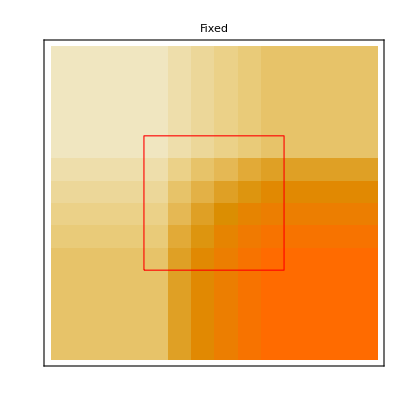
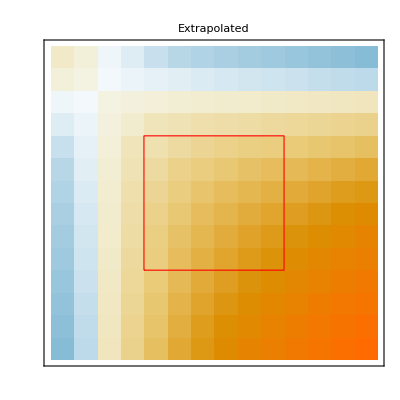
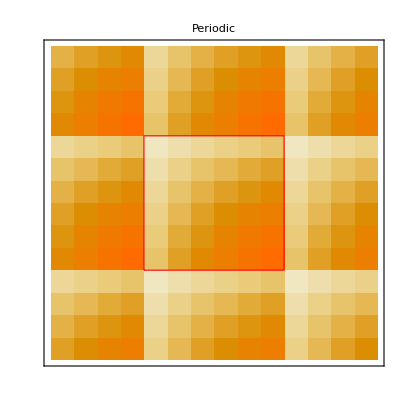
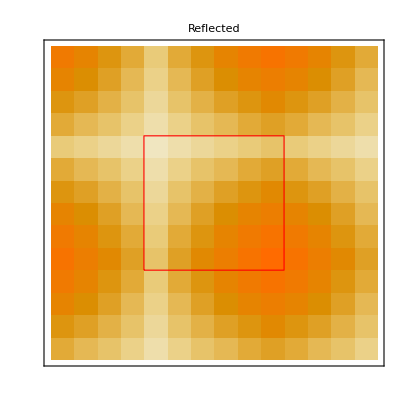
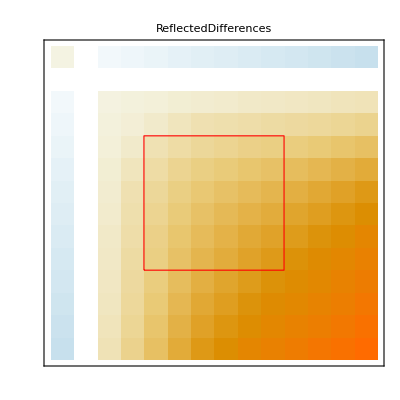
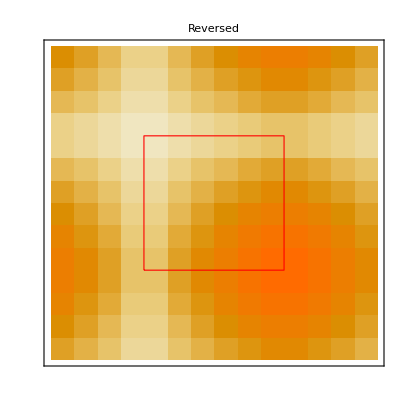
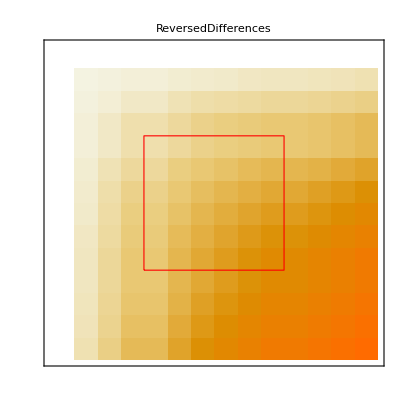
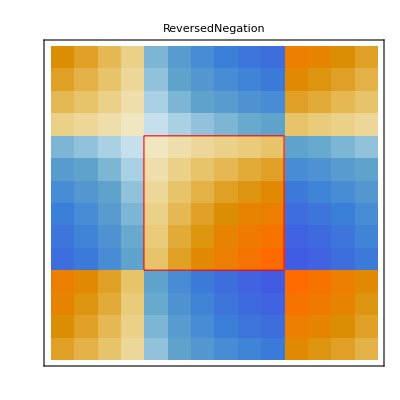

```mathematica
Table[MatrixPlot[ArrayPad[m,4,p],Epilog->{EdgeForm[{Thick,Red}],Transparent,Rectangle[{4,4},{10,10}]},FrameTicks->None,PlotLabel->p],{p,{"Fixed","Extrapolated","Periodic","Reflected","ReflectedDifferences","Reversed","ReversedDifferences","ReversedNegation"}}]
```

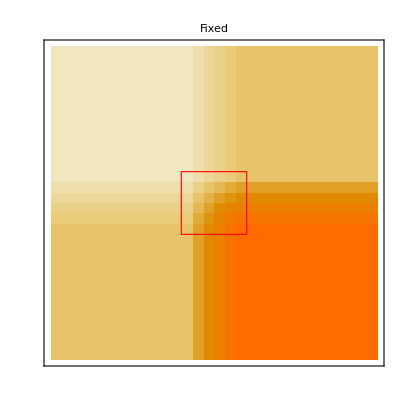
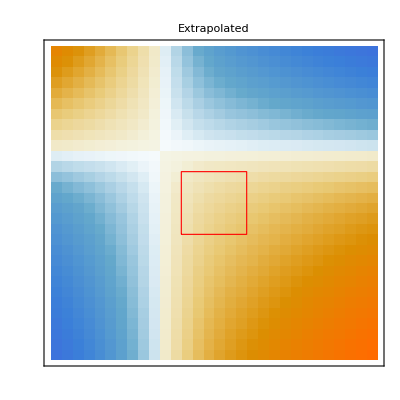
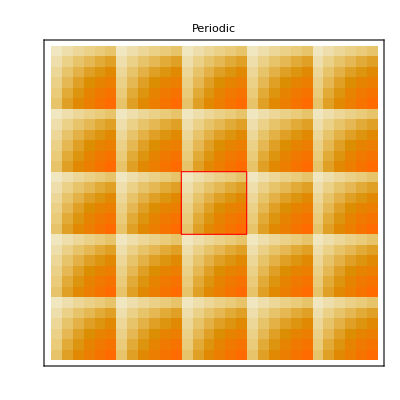
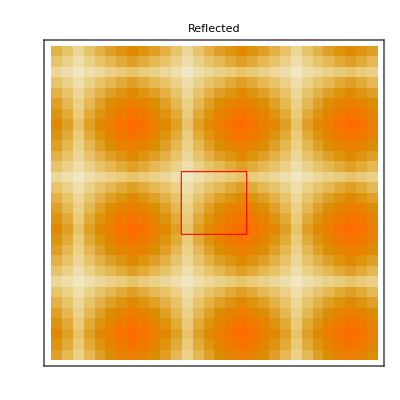
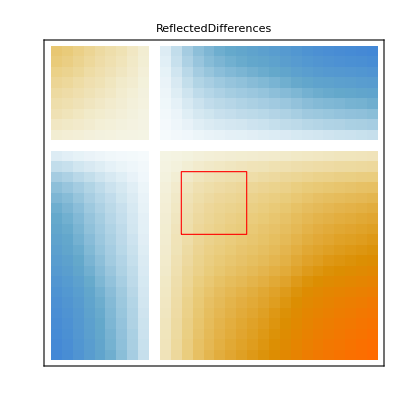
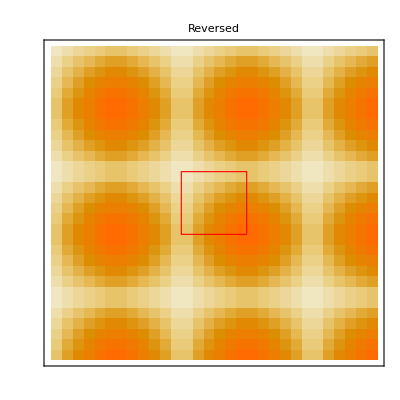
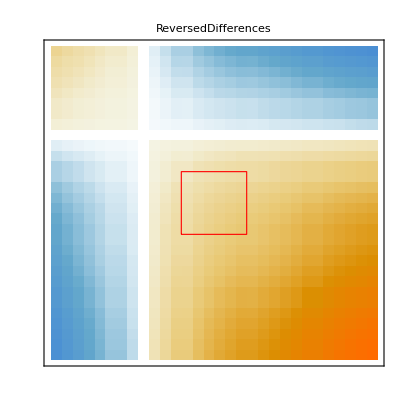
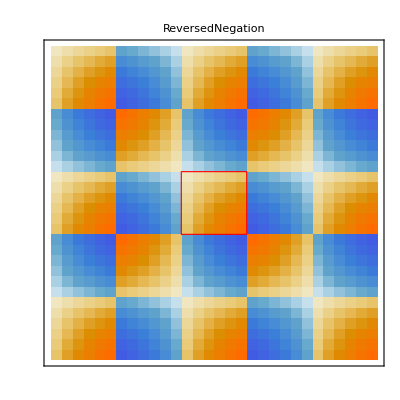

```mathematica
Table[MatrixPlot[ArrayPad[m,12,p],Epilog->{EdgeForm[{Thick,Red}],Transparent,Rectangle[{12,12},{18,18}]},FrameTicks->None,PlotLabel->p],{p,{"Fixed","Extrapolated","Periodic","Reflected","ReflectedDifferences","Reversed","ReversedDifferences","ReversedNegation"}}]
```

The padding value "Fixed" indicates that the elements added at each corner should be copies of the elements at the corners of the original array.

```mathematica
ArrayPad[m,2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | √2 | √3 | 2 | √5 | √6 | 0 | 0
0 | 0 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 0 | 0
0 | 0 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 0 | 0
0 | 0 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 0 | 0
0 | 0 | √5 | √10 | √15 | 2 √5 | 5 | √30 | 0 | 0
0 | 0 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ArrayPad[m,2,"Fixed"]//MatrixForm
```

(1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6
1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6
1 | 1 | 1 | √2 | √3 | 2 | √5 | √6 | √6 | √6
√2 | √2 | √2 | 2 | √6 | 2 √2 | √10 | 2 √3 | 2 √3 | 2 √3
√3 | √3 | √3 | √6 | 3 | 2 √3 | √15 | 3 √2 | 3 √2 | 3 √2
2 | 2 | 2 | 2 √2 | 2 √3 | 4 | 2 √5 | 2 √6 | 2 √6 | 2 √6
√5 | √5 | √5 | √10 | √15 | 2 √5 | 5 | √30 | √30 | √30
√6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6
√6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6
√6 | √6 | √6 | 2 √3 | 3 √2 | 2 √6 | √30 | 6 | 6 | 6)

## LengthWhile

```mathematica
LengthWhile[{1,1,2,3,5,8,13,21},#<10&]
```

6

Find how many primes have Fibonacci numbers less than 1000.

```mathematica
LengthWhile[Prime[Range[1000]],Fibonacci[#]<1000&]
```

6

## TakeWhile

```mathematica
TakeWhile[{2,4,6,1,2,3},EvenQ]
```

{2,4,6}

```mathematica
TakeWhile[{1,1,2,3,5,8,13,21},#<10&]
```

{1,1,2,3,5,8}

```mathematica
TakeWhile[Prime[Range[1000]],Fibonacci[#]<1000&]
```

{2,3,5,7,11,13}

I think an operator form of TakeWhile and LengthWhile could also be created.

TakeWhile[Fibonacci[#]<1000&][Prime[Range[1000]]

For example this doesn't work:

```mathematica
TakeWhile[Fibonacci[#]<1000&][Prime[Range[1000]]]//Short
```

TakeWhile[Fibonacci[#1]<1000&][{2,3,5,«994»,7901,7907,7919}]

## Ratios

```mathematica
Ratios[{b,c,d,f,g,h}]
```

{c/b,d/c,f/d,g/f,h/g}

```mathematica
Ratios[{b,c,d,f,g,h},2]
```

{(b d)/c^2,(c f)/d^2,(d g)/f^2,(f h)/g^2}

```mathematica
Ratios[{b,c,d,f,g,h},5]
```

{(c^5 f^10 h)/(b d^10 g^5)}